Using the Wolfram One Desktop tool. They offer both cloud and desktop versions.
https://www.wolfram.com/desktop/
ChatGPT is based on GPT which stands for Generative Pre-trained Transformer. GPT3 is closed. We will start with a GPT2 trained on WebText. Not perfect, but still a start to show the concepts.

```mathematica
model=NetModel[{"GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling"}]
```

NetChain[<>]

```mathematica
ReverseSort[Association@model["The best thing about AI is its ability to",{"TopProbabilities",10}]]
```

<| learn→0.0445303, predict→0.0349752, make→0.0319075, understand→0.0307803, do→0.0288511, be→0.0274695, solve→0.0254793, adapt→0.0189306, find→0.0184957, create→0.0177454|>

```mathematica
<|" learn"->0.04453028738498688," predict"->0.034975163638591766," make"->0.03190750628709793," understand"->0.03078034520149231," do"->0.028851112350821495," be"->0.02746950089931488," solve"->0.025479285046458244," adapt"->0.018930550664663315," find"->0.018495693802833557," create"->0.01774538680911064|>
```

```mathematica
Dataset[ReverseSort[Association[%]],ItemDisplayFunction->(PercentForm[#,2]&)]
```

This is just choosing the most likely value for each word. NOTE: We will get to randomness, but this is a zero temperature case - where we don’t let the model go away from the highest probability.

```mathematica
NestList[StringJoin[#,model[#,"Decision"]]&,"The best thing about AI is its ability to",6]
```

{The best thing about AI is its ability to,The best thing about AI is its ability to learn,The best thing about AI is its ability to learn from,The best thing about AI is its ability to learn from experience,The best thing about AI is its ability to learn from experience.,The best thing about AI is its ability to learn from experience. It,The best thing about AI is its ability to learn from experience. It's}

Here we will build it out for 60 words. See that it’s not very good.

```mathematica
StringReplace[Nest[StringJoin[#,model[#,"Decision"]]&,"The best thing about AI is its ability to",60],"\n".. ->" "]
```

The best thing about AI is its ability to learn from experience. It's not just a matter of learning from experience, it's learning from the world around you. The AI is a very good example of this. It's a very good example of how to use AI to improve your life. It's a very good example of

See that the probability of the word drops off at a factor if 1/n. So the first words are about 10% and the 100th word is about 1000% of a percent

```mathematica
ListLogLogPlot[Take[ReverseSort[model["The best thing about AI is its ability to","Probabilities"]],100],Frame->True]
```

-Graphics-

Let’s add in .8 setting for temperature. See how it improves!

```mathematica
Table[Nest[StringJoin[#,model[#,{"RandomSample","Temperature"->.8}]]&,"The best thing about AI is its ability to",7],5]
```

{The best thing about AI is its ability to find solutions to many problems.
,The best thing about AI is its ability to plan and perform actions east of the,The best thing about AI is its ability to speak with people. We don't,The best thing about AI is its ability to modify behavior. We can change his,The best thing about AI is its ability to make predictions and learn from the experience}

Start at the beginning: Let’s dive into the English language and understand how you might “learn” language. Starting with letters!
Wolfram has this interesting feature where it can pull in data from Wikipedia. Here we look at a Wikipedia article on cats

```mathematica
LetterCounts[WikipediaData["cats"]]
```

<|e→4338,a→3470,t→3431,i→2766,s→2636,n→2505,o→2468,r→2171,h→1640,l→1571,c→1413,d→1345,m→1000,u→931,f→772,g→756,p→654,y→607,w→524,b→521,v→399,k→217,T→115,x→86,A→83,C→82,I→69,S→55,F→42,z→40,H→36,E→36,N→31,M→29,q→29,B→28,D→27,j→22,G→22,P→21,L→17,O→17,W→16,R→14,U→14,K→9,J→8,V→5,Z→5,ṭ→4,Q→2,í→2,ä→2,ط→2,ق→2,X→1,Y→1,μ→1,ė→1,ž→1,ď→1,ö→1,đ→1,á→1,ī→1,î→1,š→1,ⲩ→1,ⲁ→1,ϣ→1|>

```mathematica
LetterCounts[WikipediaData["dogs"]]
```

<|e→3792,a→2626,o→2521,i→2486,t→2448,s→2322,n→2256,r→1791,d→1548,h→1418,l→1312,c→1050,g→909,m→828,u→766,f→628,p→619,y→487,b→453,w→401,v→390,k→145,T→84,I→80,C→78,A→73,x→68,S→65,D→58,B→47,P→39,N→38,z→36,H→27,W→26,q→25,M→24,L→24,E→23,F→21,O→21,U→20,R→18,G→17,j→15,K→10,J→7,V→7,Y→4,é→2,X→1,á→1,ó→1,ŵ→1|>

With dogs you’ll see more “o” than with cats with “a” and “t”. Let’s try with all the English language, roughly all 50,000 words - “e” is the most common letter!

```mathematica
Entity["Language","English::385w8"][EntityProperty["Language","LetterFrequency"]]
```

{e→12.7 %,t→9.06 %,a→8.17 %,o→7.51 %,i→6.97 %,n→6.75 %,s→6.33 %,h→6.09 %,r→5.99 %,d→4.25 %,l→4.03 %,c→2.78 %,u→2.76 %,m→2.41 %,w→2.36 %,f→2.23 %,g→2.02 %,y→1.97 %,p→1.93 %,b→1.49 %,v→0.978 %,k→0.772 %,j→0.153 %,x→0.15 %,q→0.095 %,z→0.074 %}

Randomly select letters based on probability. So, it will throw in more “e” than say “z”

```mathematica
With[{freq=Entity["Language", "English::385w8"][
EntityProperty["Language", "LetterFrequency"]
]},SeedRandom[53424];StringJoin[
RandomChoice[UnitConvert[Values[freq]]->Keys[freq],500]]]
```

rronoitadatcaeaesaotdoysaroiyiinnbantoioestlhddeocneooewceseciselnodrtrdgriscsatsepesdcniouhoetsedeyhedslernevstothindtbmnaohngotannbthrdthtonsipieldnleenobmesaagriladtheibduskmpoileawnruiesnnefuhomeoorndideeovnmhomosyeestnoyiatyhsdsnhbbyoaeeattoweeoonoytleyoimfannervmltrhdnsenwssatpdodtsddednrttaocaoitorntcoeeuwehcriyitihwnrapeunodchyvsurntrtlrnnlrhrsignsshtijbaeersddneeiioeeerlgtaeamihekeyaraoeplyeslcnathcuradmeetanrcsaaaevttetlmtorniiatcnttupsnrshainpphqleairakteelatweaeohemthpodssiitdtebrrni

Now we add some spacing with some probabilities as well. Using the probability that spaces are in text about 18 % of the time - you’ll see .18 in the code below.This makes it look more correct so it’s not all strung together.

```mathematica
With[{freq=Entity["Language", "English::385w8"][
EntityProperty["Language", "LetterFrequency"]
]},SeedRandom[34232];StringJoin[
RandomChoice[Append[UnitConvert[Values[freq]
],.18]->Append[Keys[freq]," "],150]]]
```

sd n oeiaim satnwhoo eer rtr ofiianordrenapwokom del oaas ill e h f rellptohltvoettseodtrncilntehtotrkthrslo hdaol n sriaefr hthehtn ld gpod a  h y oi

Word Length - Still gibbberish, but now let’s also use the probability for each “word” length before adding the space. 
1) The correct distribution of length for each word
2) The letters that have the most common occurrence
3) The spaces are distributed
Run it below.

```mathematica
SeedRandom[23424];StringJoin[Riffle[Table[
{{"[◼]", "RandomLettersWord"}}[0],{50}]," "]]
```

ni hilwhuei kjtn isjd erogofnr n rwhwfao rcuw lis fahte uss cpnc nlu oe nusaetat llfo oeme rrhrtn xdses ohm oa tne ebedcon oarvthv ist ewcrhr maedasditea yse sanetiqs bgne hen pae fnaltrda bae nesenio t omsrnohv dibiv siwcytno duohniv ctegrbiy tg eos nen tcui ioiosairim tet eonyb mc hl

Still not looking like good English, but getting more real. Remember, no smarts here. Just probabilities! We are working at the level of individual LETTERS in ENGLISH, then we’ll work towards word next.

Frequency of letters in a bar chart - Same as above just shown in graphical format

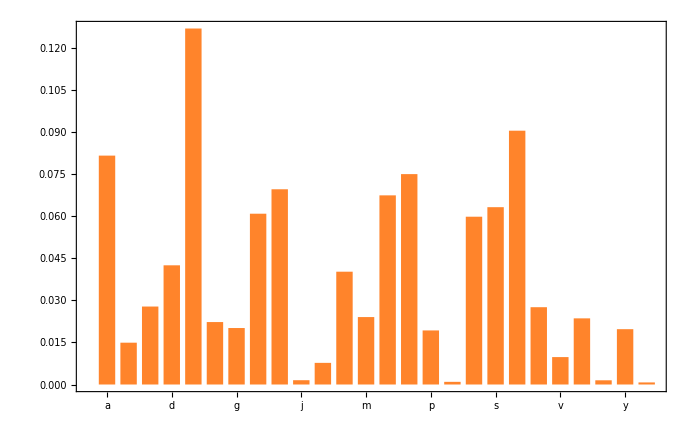

```mathematica
BarChart[Normal[Values[KeySort@Entity["Language", "English::385w8"][
EntityProperty["Language", "LetterFrequency"]
]]],ChartLabels->Alphabet[],Frame->True,
ChartStyle->Lookup[{{"[◼]", "ChatTechColors"}}["Data"],"Orange"],
ChartBaseStyle->EdgeForm[]]
```

However, if know that a “Q” has been picked, it’s not safe to say that the next will be an “E” in fact it usually a “U” “Question, “Quart”, “Quantify”, etc. What we have are 2-grams or basically “n-grams” of letters.
Let’s go ahead and plot these pairs of letters. We’re the probability for a pair of letters. See the “Q” column, you can see that it’s “u” for the next one. For “T” is an “h”, etc.

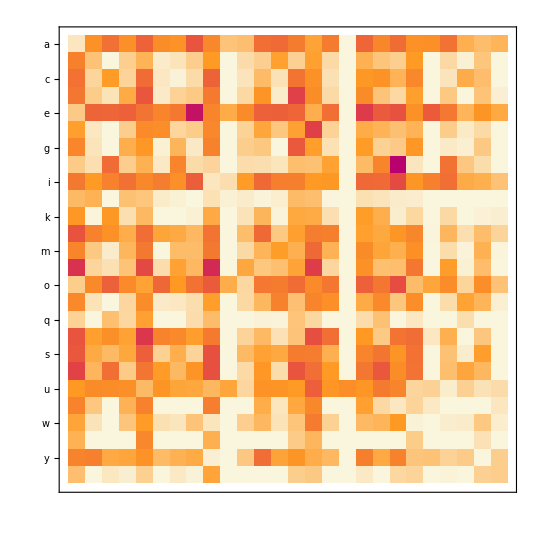

```mathematica
MatrixPlot[Transpose@With[{data=},
Outer[Lookup[Lookup[data,Key@{#1}],Key@{#2},0]&,Alphabet[],Alphabet[]]], FrameTicks->{{#,None},{None,#}}&[Table[{i,FromLetterNumber[i]},{i,26}]],
ColorFunction->{{"[◼]", "ChatTechColors"}}["Orange"]]
```

Reminder - We are just trying to generate text from the basics. Now let’s drop in the probability of of multiple letters and see what happens. We try this with combos of 2,3, 4 and 5 letters. 0 is just letters on their own, 1 is pairs of letters. However, each getting better and better! Last row actually showing real English words. This is how autocomplete works so well, if you type in “aver” it’s know that it must be “average”.

```mathematica
SeedRandom[234098234];
Grid[Table[{Style[Text@n,Lighter@Gray],
StringJoin[Riffle[Table[{{"[◼]", "RandomLettersWord"}}[n],
{12}]," "]]},{n,0,5}],FrameStyle->LightGray,
Frame->All,Alignment->Left,Spacings->{1,0.5}]
```

0 | on gxeeetowmt tsifhy ah aufnsoc ior oia itlt bnc tu ih uls
1 | ri io os ot timumumoi gymyestit ate bshe abol viowr wotybeat mecho
2 | wore hi usinallistin hia ale warou pothe of premetra bect upo pr
3 | qual musin was witherins wil por vie surgedygua was suchinguary outheydays theresist
4 | stud made yello adenced through theirs from cent intous wherefo proteined screa
5 | special average vocab consumer market prepara injury trade consa usually speci utility

Pretty cool! Let’s move from looking at letters to words. ChatGPT uses collections of characters ( called tokens - OpenAI says it roughly 4 characters for English text or 3/4 of a word - allows for suffix and prefix), but for now we’ll do a word. There are about 50,000 words in English. Here is a way to get the probability of a word.

```mathematica
WordFrequencyData["House"]
```

0.000186124

Let’s do the same thing we did with probabilities of letters with words. You’ll see we can get sentences. Here’s 30 words

```mathematica
SeedRandom[2134];StringJoin[Riffle[Table[
{{"[◼]", "WeightedRandomWord"}}[],
{30}]," "]]
```

from not emergency tree of is its are and their the rose and default cold statuesque had worth director orientation have possibly one the the used be said that little

Why can’t we just brute force this? 
We don’t have enough text to allow us to have all the possible combinations of 5 or even larger n-grams of words. 50,000 words with all combinations of just 5-n grams is more than 3 trillion.
Imagine writing an article about your favorite baseball team. You’ll generate text quite quickly that has never been generated before.

Let’s build a model!
To allow for the prediction of what word will come next! Here’s a famous example of how gravity affects an object. For example, Galileo’s dropping rocks from the tower of Pisa. We can project out to 35 floors, etc for the time for it to hit the ground as this follows a square root function.

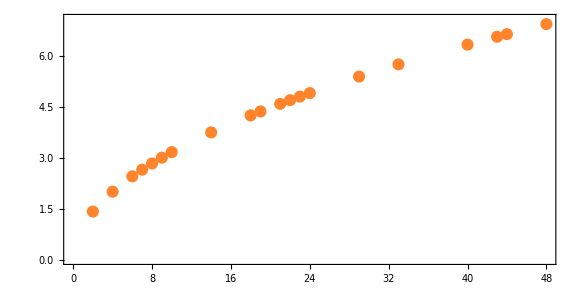

```mathematica
SeedRandom[34535];ListPlot[{#,Sqrt[#]}&/@Sort[
RandomSample[Range[50],20]],Frame->True,PlotRange->{0,Sqrt[50]},
PlotStyle->{{{"[◼]", "ChatTechColors"}}["Data"]["Orange"],
PointSize[.015]},AspectRatio->1/2]
```

Here we are just assuming a straight line

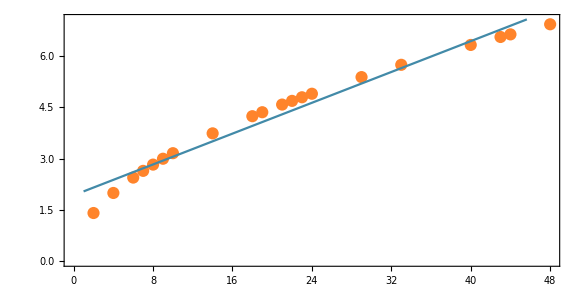

```mathematica
With[{data=(SeedRandom[34535];{#,Sqrt[#]}&/@Sort[RandomSample[Range[50],20]])},Show[ListPlot[data,Frame->True,PlotRange->{0,Sqrt[50]},PlotStyle->{{{"[◼]", "ChatTechColors"}}["Data"]["Orange"],
PointSize[.015]},AspectRatio->1/2],Plot[Evaluate[Fit[data,{1,x},x]],{x,1,50},
PlotRange->{0,Sqrt[50]},
PlotStyle->{{"[◼]", "ChatTechColors"}}["Data"]["Teal"]]]]
```

This below actually a better match though. By using  a quadratic curve.

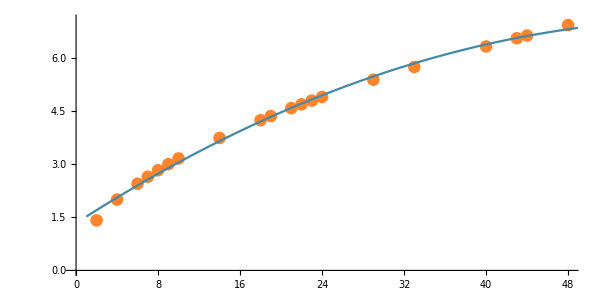

```mathematica
With[{data=(SeedRandom[34535];{#,Sqrt[#]}&/@Sort[RandomSample[Range[50],20]])},Show[ListPlot[data,Frame->T
rue,PlotRange->{0,Sqrt[50]},PlotStyle->{{{"[◼]", "ChatTechColors"}}["Data"]["Orange"],
PointSize[.015]},AspectRatio->1/2],Plot[Evaluate[Fit[data,{1,x,x^2},x]],{x,1,50},
PlotRange->{0,Sqrt[50]},
PlotStyle->{{"[◼]", "ChatTechColors"}}["Data"]["Teal"]
]]]
```

However, to reinforce the previous point, with language there is no single mathematical formula that we can use to solve our problem. So this is where we need to approach the solution by looking at how humans have solved problems where there is no one function.

LET’S LOOK AT COMPUTER VISION! It can provide some details. Here’s some easy numbers to deal with looking at each pixel and making a prediction.

```mathematica
Append[Table[{{"[◼]", "DigitArrayPlot"}}[n],{n,0,5}],"…"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,…}

```mathematica
{{"[◼]", "DigitArrayPlot"}}[Style[4,FontFamily->#]]&/@{"Bodoni 72","Didot","Fira Sans","Gotham","Papyrus", "ComicSans"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Neural Nets were conceived back in the 1940’s. Seem to be a simple idealization of how we think the human brain works. Each neuron uses electrical signals to pass information from our photoreceptors and then passed through the network for us to “recognize” an object. Nothing special about  LeNet trained on MNIST data. It was constructed back in 1998 and found to work. Used by post office, banks, etc for handwritten recognition of values.

Computers are good at seeing things that it has seen before. They all match here. We are just using a basic neural net and hand written data set from MNIST. MNIST Database of Handwritten Digits, consisting of 60,000 grayscale images of size 28x28.

```mathematica
NetModel["LeNet Trained on MNIST Data"][{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{7,0,9,7,8,2,4,1,1,1}

Here’s a picture of a Neural Network.

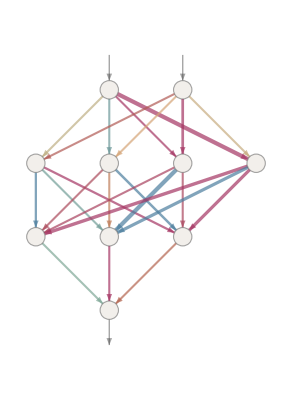

```mathematica
{{"[◼]", "NetGraphPlot"}}[{{"[◼]", "PointRankData2D"}}["Result431"],"AddArrows"->True]
```

These are examples of weights being passed through the neural network. Each is tuned and adjusted over time as it learns. The value of a given neuron is determined by multiplying the values of “previous neurons” by their corresponding weights, then adding these up and adding a constant—and finally applying a “thresholding” (or “activation”) function.

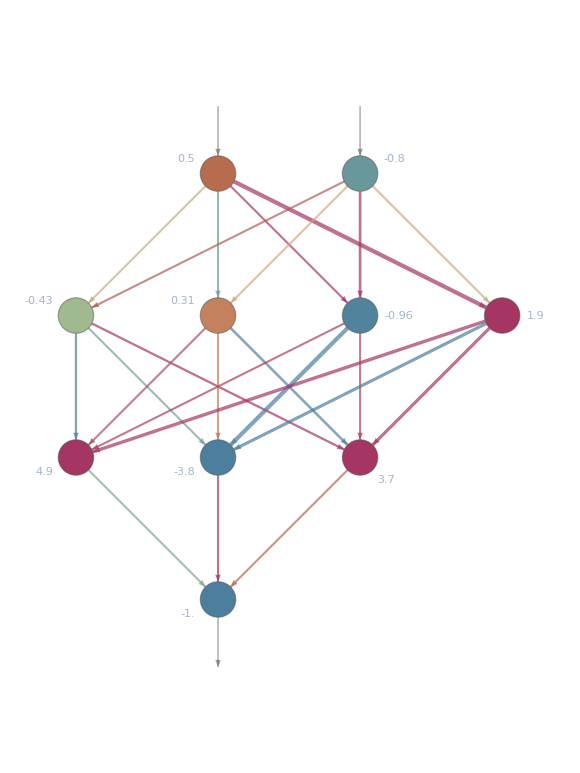

```mathematica
{{"[◼]", "NetGraphPlot"}}[{{"[◼]", "PointRankData2D"}}["Result431"],{.5,-.8},"AddArrows"->True]
```

How Does a Neural Net Work?
Here’s a very simple function. The computer doesn’t know this though!

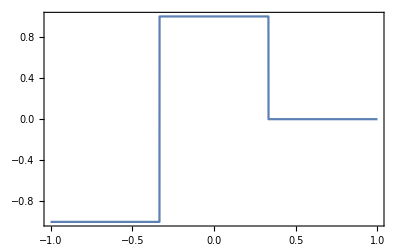

```mathematica
Plot[Piecewise[{{-1,x<-1/3},{1,-1/3<x<1/3},{0,x>1/3}}],{x,-1,1},Exclusions->None,Frame->True,PlotRangePadding->.2]
```

Let’s try and have an empty neural network try and figure it out.

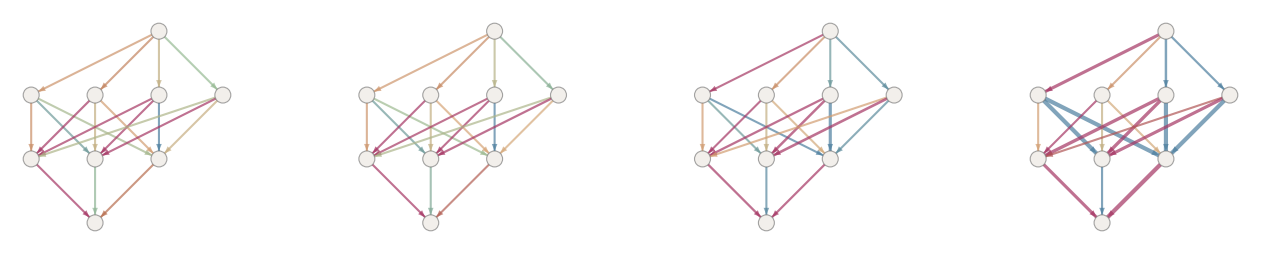

```mathematica
GraphicsGrid[{{"[◼]", "CompositeLossPlot"}}[{{"[◼]", "PiecewiseData1D"}}],ImageSize->1000,Dividers->{{False,{True},False}},FrameStyle->LightGray,Spacings->{45,Automatic}]
```

This is how we try to minimize the loss function and finally with the dots it gets closer and closer as we tweak the weights to reduce the loss and get closer to where we want to get closer to the right answer.

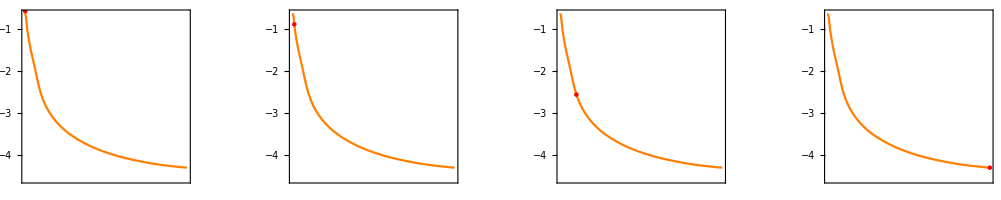

```mathematica
GraphicsGrid[{{"[◼]", "CompositeLossPlot"}}[{{"[◼]", "PiecewiseData1D"}},"ShowLoss"->True],ImageSize->600,Alignment->Center,Dividers->{{False,{True},False}},FrameStyle->LightGray,Spacings->{15,-10}]
```

Even though Neural Nets were actually originally thought about in the 40’s. It wasn’t until the 80’s when we started to see layering of neural nets. Then GPU’s in 2012 where we could finally do training and use deep neural nets.

IMPORTANT TO NOTE: Ultimately, every neural net just corresponds to some overall mathematical function—though it may be messy to write out. The neural net of ChatGPT also just corresponds to a mathematical function like this—but effectively with BILLIONS of terms. For the example above, it would be:

```mathematica
{{"[◼]", "NetToFunction"}}[{{"[◼]", "PointRankData2D"}}["Result431"],{x,y},{w,b}][[-1,1]]/.Ramp->f//TraditionalForm
```

w511 f(w311 f(b11+x w111+y w112)+w312 f(b12+x w121+y w122)+w313 f(b13+x w131+y w132)+w314 f(b14+x w141+y w142)+b31)+w512 f(w321 f(b11+x w111+y w112)+w322 f(b12+x w121+y w122)+w323 f(b13+x w131+y w132)+w324 f(b14+x w141+y w142)+b32)+w513 f(w331 f(b11+x w111+y w112)+w332 f(b12+x w121+y w122)+w333 f(b13+x w131+y w132)+w334 f(b14+x w141+y w142)+b33)+b51

How Do We Train a Neural Net?
Let’s try and train our own on the hand written text.
What happens with ChatGPT is that you can look at a series of words and then mask out the following words and see how close ChatGPT was to getting it right. You then train the model and tweak the weights to get it closer to the right answer.

Look at dataset from MNIST - written text of about 10,000 integers. Here we take 500 samples and train on it.

```mathematica
RandomSample[ResourceData["MNIST"],500]
```

{-Graphics-→2,-Graphics-→3,-Graphics-→5,-Graphics-→1,-Graphics-→1,-Graphics-→0,-Graphics-→9,-Graphics-→9,-Graphics-→8,-Graphics-→2,-Graphics-→5,-Graphics-→0,-Graphics-→2,-Graphics-→9,-Graphics-→3,-Graphics-→4,-Graphics-→5,-Graphics-→9,-Graphics-→3,-Graphics-→6,-Graphics-→9,-Graphics-→7,-Graphics-→9,-Graphics-→6,-Graphics-→3,-Graphics-→8,-Graphics-→3,-Graphics-→1,-Graphics-→2,-Graphics-→7,-Graphics-→7,-Graphics-→4,-Graphics-→2,-Graphics-→6,-Graphics-→1,-Graphics-→8,-Graphics-→6,-Graphics-→9,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→5,-Graphics-→2,-Graphics-→0,-Graphics-→8,-Graphics-→7,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→8,-Graphics-→9,-Graphics-→4,-Graphics-→5,-Graphics-→2,-Graphics-→3,-Graphics-→1,-Graphics-→0,-Graphics-→1,-Graphics-→4,-Graphics-→5,-Graphics-→1,-Graphics-→9,-Graphics-→4,-Graphics-→7,-Graphics-→1,-Graphics-→3,-Graphics-→9,-Graphics-→9,-Graphics-→7,-Graphics-→5,-Graphics-→5,-Graphics-→6,-Graphics-→5,-Graphics-→1,-Graphics-→4,-Graphics-→5,-Graphics-→7,-Graphics-→5,-Graphics-→4,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→8,-Graphics-→7,-Graphics-→8,-Graphics-→6,-Graphics-→6,-Graphics-→5,-Graphics-→3,-Graphics-→1,-Graphics-→2,-Graphics-→6,-Graphics-→6,-Graphics-→2,-Graphics-→3,-Graphics-→6,-Graphics-→2,-Graphics-→3,-Graphics-→5,-Graphics-→1,-Graphics-→0,-Graphics-→4,-Graphics-→0,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→7,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→5,-Graphics-→5,-Graphics-→0,-Graphics-→2,-Graphics-→6,-Graphics-→6,-Graphics-→6,-Graphics-→6,-Graphics-→6,-Graphics-→5,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→9,-Graphics-→1,-Graphics-→8,-Graphics-→7,-Graphics-→4,-Graphics-→1,-Graphics-→5,-Graphics-→2,-Graphics-→4,-Graphics-→0,-Graphics-→2,-Graphics-→9,-Graphics-→2,-Graphics-→3,-Graphics-→7,-Graphics-→8,-Graphics-→7,-Graphics-→3,-Graphics-→0,-Graphics-→0,-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→7,-Graphics-→7,-Graphics-→9,-Graphics-→2,-Graphics-→2,-Graphics-→8,-Graphics-→6,-Graphics-→1,-Graphics-→9,-Graphics-→1,-Graphics-→4,-Graphics-→6,-Graphics-→2,-Graphics-→9,-Graphics-→8,-Graphics-→3,-Graphics-→7,-Graphics-→7,-Graphics-→2,-Graphics-→7,-Graphics-→7,-Graphics-→4,-Graphics-→0,-Graphics-→4,-Graphics-→8,-Graphics-→5,-Graphics-→9,-Graphics-→2,-Graphics-→4,-Graphics-→7,-Graphics-→3,-Graphics-→8,-Graphics-→4,-Graphics-→9,-Graphics-→4,-Graphics-→0,-Graphics-→4,-Graphics-→7,-Graphics-→8,-Graphics-→5,-Graphics-→2,-Graphics-→8,-Graphics-→3,-Graphics-→5,-Graphics-→0,-Graphics-→6,-Graphics-→3,-Graphics-→9,-Graphics-→7,-Graphics-→7,-Graphics-→3,-Graphics-→2,-Graphics-→5,-Graphics-→9,-Graphics-→0,-Graphics-→2,-Graphics-→1,-Graphics-→0,-Graphics-→8,-Graphics-→3,-Graphics-→9,-Graphics-→6,-Graphics-→9,-Graphics-→1,-Graphics-→9,-Graphics-→0,-Graphics-→8,-Graphics-→6,-Graphics-→2,-Graphics-→8,-Graphics-→1,-Graphics-→8,-Graphics-→4,-Graphics-→0,-Graphics-→8,-Graphics-→3,-Graphics-→1,-Graphics-→9,-Graphics-→3,-Graphics-→8,-Graphics-→2,-Graphics-→5,-Graphics-→2,-Graphics-→5,-Graphics-→2,-Graphics-→8,-Graphics-→8,-Graphics-→9,-Graphics-→9,-Graphics-→3,-Graphics-→0,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→1,-Graphics-→2,-Graphics-→8,-Graphics-→3,-Graphics-→8,-Graphics-→8,-Graphics-→7,-Graphics-→0,-Graphics-→3,-Graphics-→4,-Graphics-→6,-Graphics-→7,-Graphics-→4,-Graphics-→0,-Graphics-→4,-Graphics-→8,-Graphics-→7,-Graphics-→1,-Graphics-→9,-Graphics-→5,-Graphics-→0,-Graphics-→7,-Graphics-→2,-Graphics-→0,-Graphics-→6,-Graphics-→8,-Graphics-→3,-Graphics-→2,-Graphics-→0,-Graphics-→7,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→7,-Graphics-→8,-Graphics-→3,-Graphics-→8,-Graphics-→6,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→6,-Graphics-→5,-Graphics-→2,-Graphics-→7,-Graphics-→6,-Graphics-→3,-Graphics-→6,-Graphics-→8,-Graphics-→5,-Graphics-→2,-Graphics-→8,-Graphics-→3,-Graphics-→3,-Graphics-→0,-Graphics-→4,-Graphics-→2,-Graphics-→7,-Graphics-→4,-Graphics-→5,-Graphics-→4,-Graphics-→6,-Graphics-→0,-Graphics-→4,-Graphics-→1,-Graphics-→7,-Graphics-→1,-Graphics-→9,-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→0,-Graphics-→8,-Graphics-→7,-Graphics-→1,-Graphics-→1,-Graphics-→3,-Graphics-→7,-Graphics-→9,-Graphics-→1,-Graphics-→1,-Graphics-→7,-Graphics-→2,-Graphics-→3,-Graphics-→6,-Graphics-→3,-Graphics-→0,-Graphics-→3,-Graphics-→5,-Graphics-→8,-Graphics-→9,-Graphics-→3,-Graphics-→5,-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→6,-Graphics-→0,-Graphics-→7,-Graphics-→1,-Graphics-→8,-Graphics-→7,-Graphics-→4,-Graphics-→2,-Graphics-→6,-Graphics-→2,-Graphics-→7,-Graphics-→8,-Graphics-→9,-Graphics-→5,-Graphics-→4,-Graphics-→5,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→0,-Graphics-→9,-Graphics-→8,-Graphics-→9,-Graphics-→2,-Graphics-→6,-Graphics-→2,-Graphics-→6,-Graphics-→1,-Graphics-→9,-Graphics-→1,-Graphics-→3,-Graphics-→3,-Graphics-→9,-Graphics-→2,-Graphics-→5,-Graphics-→4,-Graphics-→6,-Graphics-→6,-Graphics-→1,-Graphics-→8,-Graphics-→2,-Graphics-→0,-Graphics-→2,-Graphics-→7,-Graphics-→8,-Graphics-→9,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→7,-Graphics-→0,-Graphics-→4,-Graphics-→7,-Graphics-→3,-Graphics-→1,-Graphics-→6,-Graphics-→9,-Graphics-→8,-Graphics-→5,-Graphics-→5,-Graphics-→3,-Graphics-→8,-Graphics-→9,-Graphics-→3,-Graphics-→4,-Graphics-→5,-Graphics-→2,-Graphics-→1,-Graphics-→9,-Graphics-→9,-Graphics-→0,-Graphics-→6,-Graphics-→7,-Graphics-→4,-Graphics-→6,-Graphics-→1,-Graphics-→7,-Graphics-→8,-Graphics-→6,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→1,-Graphics-→6,-Graphics-→2,-Graphics-→3,-Graphics-→0,-Graphics-→4,-Graphics-→1,-Graphics-→8,-Graphics-→0,-Graphics-→3,-Graphics-→1,-Graphics-→1,-Graphics-→8,-Graphics-→9,-Graphics-→8,-Graphics-→9,-Graphics-→5,-Graphics-→7,-Graphics-→8,-Graphics-→1,-Graphics-→2,-Graphics-→5,-Graphics-→7,-Graphics-→7,-Graphics-→7,-Graphics-→1,-Graphics-→8,-Graphics-→2,-Graphics-→6,-Graphics-→8,-Graphics-→3,-Graphics-→1,-Graphics-→8,-Graphics-→5,-Graphics-→6,-Graphics-→1,-Graphics-→8,-Graphics-→3,-Graphics-→5,-Graphics-→5,-Graphics-→4,-Graphics-→9,-Graphics-→7,-Graphics-→8,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→0,-Graphics-→9,-Graphics-→9,-Graphics-→1,-Graphics-→5,-Graphics-→1,-Graphics-→1,-Graphics-→9,-Graphics-→2,-Graphics-→8,-Graphics-→2,-Graphics-→1,-Graphics-→9,-Graphics-→9,-Graphics-→5,-Graphics-→1,-Graphics-→0,-Graphics-→0,-Graphics-→2,-Graphics-→4,-Graphics-→8,-Graphics-→7,-Graphics-→3,-Graphics-→8,-Graphics-→7,-Graphics-→6,-Graphics-→9,-Graphics-→1}

Train our own NeuralNet and watch the loss going down. Super simple example of how to train an NeuralNet with 2000 examples and then predict the text. Gets it at 100%

```mathematica
NetTrain[NetModel["LeNet"],%]
```

NetChain[<>]

```mathematica
%[-Graphics-]
```

4

Let’s look at the probabilities for the answer of each letter. 0 element is 0, next is 1, etc.

```mathematica
SoftmaxLayer[][Drop[%75,-1][-Graphics-]]
```

{5.65037×10^-10,2.11554×10^-12,1.70562×10^-8,3.80092×10^-12,0.99999,8.89791×10^-9,2.11054×10^-8,4.28486×10^-10,3.43043×10^-9,9.51146×10^-6}

Let’s back up 1 layer in the neural net and see where things are at before the final decision. Look at this layer. They show the signature of “4-ness” of what kind of thing we are seeing. And we can keep shifting back more and more layers.

```mathematica
Drop[%75,-1][-Graphics-]
```

{-5.07515,-10.6627,-1.66777,-10.0768,16.219,-2.31847,-1.45475,-5.35178,-3.2716,4.65597}

This is the key to attention! When we “nailed the task” we can backup and look and see what was the signature we can see earlier in the network the signature. See below how these images live in dimensional space.

There is something going on with putting these into dimensional space with each pixel in the image.

```mathematica
FeatureSpacePlot3D[SeedRandom[123];#->SetAlphaChannel[#,ColorNegate[#]]&@@@RandomSample[ResourceData["MNIST"],50],FeatureExtractor->NetDrop[NetModel["LeNet Trained on MNIST Data"],-3]]
```

-Graphics3D-

Can we do this with words? Turns out that YES we can! We do this with “Embeddings”. Words that have a similar meaning are put in to the same dimensional space. This is how we represent words with numbers. This is just 2 dimensional. Roughly though the same thing we did with the images of numbers above.
Let’s recall all we are trying to do is predict the next word.

-Graphics-
Can also derive meaning for example ( Berlin - Germany + France = Paris )
-Graphics-

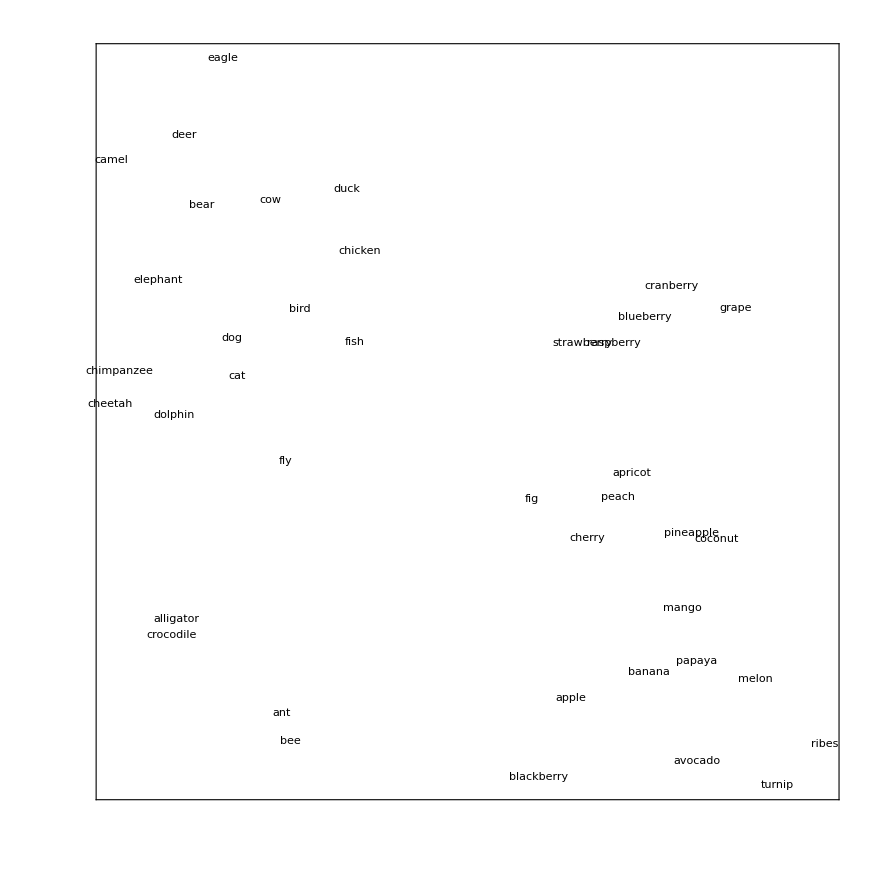

```mathematica
FeatureSpacePlot[{"alligator","ant","bear","bee","bird","camel","cat","cheetah","chicken","chimpanzee","cow","crocodile","deer","dog","dolphin","duck","eagle","elephant","fish","fly","apple","apricot","avocado","banana","blackberry","blueberry","cherry","coconut","cranberry","grape","turnip","mango","melon","papaya","peach","pineapple","raspberry","strawberry","ribes","fig"},FeatureExtractor->NetModel["GloVe 300-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"],Frame->True,FrameTicks->None]
```

Computers work much better with numbers. Embeddings are just a number representing word pairs. Here’s an example below. You can assign each word in the 50,000 words a unique number. However, we need to store them in dimensional space. Each word is represented as a matrix.

We can look at the feature vectors and projecting them to 2-dimensional space to see how similar they are. We are looking at what makes a “cat” and “dog” be a choice by the network vs using the word “chair”. Can’t tell that cat and dog are close to each other, but a computer can. NOTE: ChatGPT uses chunks of words, rather than specific words, but the concept is the same.

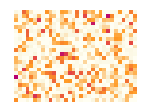
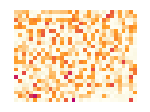
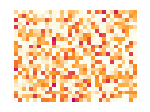
{-Graphics-cat,-Graphics-dog,-Graphics-chair}

```mathematica
Labeled[ArrayPlot[Partition[
First[NetExtract[NetModel["GPT2 Transformer Trained on WebText Data"],{"embedding","embeddingtokens"}][NetExtract[NetModel["GPT2 Transformer Trained on WebText Data"],"Input"][#]]],32],Frame->None,ImageSize->150,ColorFunction->{{"[◼]", "ChatTechColors"}}["Orange"]],#]&/@{"cat","dog","chair"}
```

Embedding Vector Example:
CAT = {{-0.0802898,0.0340174,-0.49889,0.0117027,0.019475,-0.174645,0.384173,-0.0108258,-0.184527,0.127755,..}}
DOG = {{-0.102029,-0.0657201,-0.32943,-0.0616078,-0.00910606,-0.160064,0.317742,-0.202682,-0.178742,0.011637,..}}
CHAIR = {{-0.145438,-0.123598,-0.279552,-0.0516923,-0.0281756,-0.307468,1.21536,-0.190257,-0.216411,...}}

But actually we can go further than just characterizing words by collections of numbers; we can also do this for sequences of words, or indeed whole blocks of text. Inside ChatGPT that’s how it’s dealing with things.

Steps:
1. It takes the text it’s got so far, and generates an embedding vector to represent it. 
2. Then its goal is to find the probabilities for different words that might occur next by feeding it through the neural network.
3. After generating the next token, that value is added to the prior token.
4. Go back to #1

Using these embeddings and previous passes it knows which words should be paid attention. This is interesting since the neural net starts to learn the underlying structure if what language is!

We do know that human language has structure. ChatGPT has actually been able to show that there is more regularity than we thought was there and has learned it! ChatGPT has learned syntactic grammar.

```mathematica
First[TextStructure["The best thing about AI is its ability to learn from experience.","ConstituentGraphs"]]
```

-Graphics-

ChatGPT has learned meaningful sequences. Patterns of word usage and you could substitute in different words to come to the same conclusion. People say that ChatGPT is “figuring it out”, but it’s really just using similar word placement because it’s seen that it can. It’s following a templated structure of logic.

Let’s See How ChatGPT is Moving Through The Sentence
This graph shows how it moves around and hops from one to another.

```mathematica
Module[{step, promptcolor,color,result,vocabulary,i=1}, 
vocabulary = NetExtract[NetExtract[NetModel[{"GPT2 Transformer Trained on WebText Data", "Task" -> "LanguageModeling"}], "Output"], "Labels"];
result=;
promptcolor = {{"[◼]", "ChatTechColors"}}["Normal"][0.2];
color = {{"[◼]", "ChatTechColors"}}["Normal"][-1];
step = result["PromptLength"] + Replace[i, {Automatic -> result["ContinuationLength"], 
       n_Integer :> Clip[n, {1, result["ContinuationLength"]}]}]; 
 
Show[ListPlot[{Thread[Callout[result["Points"][[1 ;; result["PromptLength"],-1]], 
        result["Tokens"][[1 ;; result["PromptLength"]]]]], 
     Thread[Callout[result["Points"][[result["PromptLength"] + 1 ;; step,-1]], 
        result["Tokens"][[result["PromptLength"] + 1 ;; step]]]], 
      Thread[Callout[result["Points"][[step,1 ;; -2]], 
        Thread[Style[vocabulary[[result["BestPositions"][[step,1 ;; -2]]]], 
          Opacity[0.5]]]]]}, PlotStyle -> {promptcolor, color, 
       Directive[Black, Opacity[0.3]]}], 
    Graphics[{{PointSize[0.01], {promptcolor, Point[result["PromptPoints"][[1]]]}, 
       {color, Point[result[["Points",step - 1,-1]]]}, 
       Point[result[["Points",step,-1]]]}, {{promptcolor, AbsoluteThickness[1.5], 
        Line[result["PromptPoints"]]}, {color, AbsoluteThickness[2], 
        Line[Take[result[["Points",All,-1]], {result["PromptLength"], step - 1}]]}}, 
      Arrowheads[0.02], MapThread[{Opacity[#2 + 0.1], AbsoluteThickness[2*#2], 
         Arrow[{result[["Points",step - 1,-1]], #1}]} & , {result[["Points",step]], 
        Rescale[result[["Probabilities",step]]]}]}], PlotRange->Automatic, ImageSize -> Medium, 
    Frame -> True, FrameTicks -> False, Axes -> None, PlotRange -> result["Range"], 
    PlotRangePadding -> Scaled[0.05]]]
```

-Graphics-

Here is how it “fans out” as it goes from each word to word

```mathematica
With[{fun=Function[Module[{step,promptcolor,color,result,i=#},
 promptcolor = {{"[◼]", "ChatTechColors"}}["Normal"][.2]; color = RGBColor[{15, 162, 127}/255];
result=;step = result["PromptLength"] + Replace[i, {Automatic -> result["ContinuationLength"
			], n_Integer :> Clip[n, {1, result["ContinuationLength"]}]}];
		Labeled[Show[
			Graphics[{{PointSize[0.01], {promptcolor, Point[result[
			"PromptPoints"][[1]]]}, {color, Point[result[["Points", step - 1, -1]]
			]}, Point[result[["Points", step, -1]]]}, {{promptcolor, AbsoluteThickness[
			1.5], Line[result["PromptPoints"]]}, {color, AbsoluteThickness[2], Line[
			Take[result[["Points", All, -1]], {result["PromptLength"], step - 1}]
			]}}, Arrowheads[0.02], MapThread[{ Opacity[#2 + 0.1], AbsoluteThickness[
			2 * #2], Arrow[{result[["Points", step - 1, -1]], #1}]}&, {result[["Points",
			 step]], Rescale[result[["Probabilities", step]]]}]},  PlotRange -> result["Range"], PlotRangePadding -> Scaled[0.05], Frame
			 -> True, FrameTicks -> None, AspectRatio->1/GoldenRatio
			 ],
			 ListPlot[
				{Callout[result["Points"][[step, -1]], result["Tokens"][[step]]],
				PlotStyle -> {{"[◼]", "ChatTechColors"}}["Normal"][.5]},PlotRange -> result["Range"]
			]
		], Style["…"<>result["Tokens"][[step-3;;step-1]], "Label"],Top]
	]]},
GraphicsGrid[Partition[Map[fun,Range[12]],3],ImageSize->600,Spacings->{0,20}]
]
```

-Graphics-

Finally we can then look at it in 3D space. Green is what it chose, but grey is what it considered. As you move through words you are moving through space.

```mathematica
With[{resultsGPT2=},
Graphics3D[{{AbsoluteThickness[2],{{"[◼]", "ChatTechColors"}}["Normal"][0.2],
Line[MapIndexed[Append[#1,First[#2]]&,resultsGPT2⟦"PromptPoints"⟧]]},Table[{{Black,
Table[{AbsoluteThickness[2],Opacity[resultsGPT2⟦"Probabilities",i,j⟧+0.03],Line[{Append[resultsGPT2⟦"Points",i-1,-1⟧,i-1],Append[resultsGPT2⟦"Points",i,j⟧,i]}]},{j,resultsGPT2["Continuations"]-1}]},{RGBColor[1/255 {15,162,127}],AbsoluteThickness[2],Line[{Append[resultsGPT2⟦"Points",i-1,-1⟧,i-1],Append[resultsGPT2⟦"Points",i,-1⟧,i]}]}},{i,resultsGPT2["PromptLength"]+1,resultsGPT2["PromptLength"]+resultsGPT2["ContinuationLength"]}]},BoxRatios->{1,1,GoldenRatio},ViewPoint->{-1.5,-3,2},ViewVertical->{-1,0,0}]]
```

-Graphics3D-

SUMMARY

I’ve skipped a lot of the underlying complex math - on purpose.

Overview:
1. Reviewed that you can build basic language from just probabilities or letters, spaces and what should follow.
2. Follows then that you can do the same with words ( and tokens ).
2. Using n-grams only get you so far though.
	2a. There is no way to “brute force” the generation of text.
	2b. Not enough text to have seen every possible combination.
3. To get it to work we need to take concepts from Computer Vision
	3a. Build a Neural Net
	3b. Create word embeddings to model language
	3c. Transformer Architecture - allows using self-attention to capture the relationships looking back in the sequence, then feeding it forward through the Neural Net.

In the end:
1. We discovered in building GPT  that using computation we can put together sentences and semantic grammar that it can learn language design. In the same way we have taught computers to learn Chess and Go.
2. However, in the same way we have taught computers to learn games like Chess and Go, it does better when it’s been coaxed. OpenAI added an additional layer specifically with ChatGPT that we didn’t talk about - Applied Reinforcement Learning with Human Feedback (RLHF) to help steer the answers. This is fine-tuning or “hints” that allow for a conversational context.